# OCR for Sheet Music

## Final Project for the Wolfram Summer School 2019

## Daniel Csillag

```mathematica
ClearAll["Global`*"]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/daniel/WSS19/MusicOCR

## Task Description

Given an image of some sheet music, generate some internal representation of it that can then be played, reprinted or exported to some external musical notation software.

## How we did it

The solution used is a mixture of classical computer vision techniques, machine learning techniques and parsing algorithms.
First, we use a morphological transformation to detect the staff lines, find groupings of five of them, find the distance between each line in the staff and split the sheet music into subimages with the lines removed for each staff. Then, we use a SegNet trained on the DeepScores dataset (after some preprocessing) to find bounding boxes for each musical symbol in the score; this is then passed to a LeNet to classify each symbol and another to classify rhythm for the note heads. Finally, this is passed to a parser that generates the sheet music representation.

## Datasets

Two datasets were used for this project:

DeepScores Segmentation Dataset

https://drive.google.com/drive/folders/1KFxqi0rO-bJrd03rLk87fF1iOmnjpaoG

DeepScores Classification Dataset

https://drive.google.com/file/d/1bdBrX0dAX734I3MA_ 6-wH_-N2eqq_tf _/view

## Loading the Datasets

These are some functions to load the datasets:

### SegNet

```mathematica
loadDataOutOfCore[path_String?DirectoryQ] := Flatten[MapThread[File[#⟦1⟧]->File[#⟦2⟧]&/@Thread[{#1,#2}&[FileNames[All,#1],FileNames[All,#2]]]&,
{FileNames[All,FileNameJoin[{path,"images_png"}]],FileNames[All,FileNameJoin[{path,"pix_annotations_png"}]]}],1]
```

### Symbol Classifier

```mathematica
min[All,x_Integer] := x
min[x_Integer,y_Integer] := Min[x,y]
```

```mathematica
importDeepScoresSymbolDataset[inputPath_String?DirectoryQ,nFiles_Integer?Positive,nSymbols_] := Flatten[(symbolPath↦(
(*Center: (15,15)*)
If[MemberQ[{"augmentationDot"},FileNameTake[symbolPath]],
{},
{rowspan,colspan}=Switch[FileNameTake[symbolPath],

];
(ImageResize[ImageTake[ImageResize[#,{256,256}],4rowspan+1,4colspan],{64,64}]->FileNameTake[symbolPath]&/@Flatten[ImagePartition[Import[#],{120,220}],1]&)
/@RandomSample[FileNames[All,symbolPath],min[nFiles,Length@FileNames[All,symbolPath]]]
]
))/@Select[Take[FileNames[All,inputPath],nSymbols],DirectoryQ]]
```

## Getting Some Example Sheet Music

```mathematica
exampleSheetMusic=-Graphics-;
```

## Preparing the Sheet Music

## Detecting the Staff Lines

Staff lines are long horizontal and thin. They can be detected by using a bottom hat transform with a short kernel. Then, by looking for close groups of five lines, we can extract an image for each staff in the original score.

Find the lines and return a list of the images of the staffs along with the median distance between the staff lines:

```mathematica
(*Crop the segmented image along with the original one.*)
detectStaffLineImages[image_,segmentized_] := Module[{
staffLines =Select[ImageLines[BottomHatTransform[image,BoxMatrix[{1,0}]],Automatic,0.0065]⟦All,1⟧,(Abs@VectorAngle[Subtract@@#,{-1,0}]<10°)&]
},
Δ =Median@Differences@Sort@Map[Mean,staffLines⟦All,All,2⟧];
staffLineGroups=Gather[Sort[staffLines,(Last@Mean@#1>Last@Mean@#2)&],(Last@Mean@#1-Last@Mean@#2<5Δ)&];
{Map[
ImageTrim[image,Flatten[#,1],{0,4Δ}]&,
staffLineGroups
],Map[
ImageTrim[segmentized,Flatten[#,1],{0,4Δ}]&,
staffLineGroups
],Δ}
]
```

```mathematica
(*only the original image.*)
detectStaffLineImages[image_] := Module[{
staffLines =Select[ImageLines[BottomHatTransform[image,BoxMatrix[{1,0}]],Automatic,0.0065]⟦All,1⟧,(Abs@VectorAngle[Subtract@@#,{-1,0}]<10°)&]
},
Δ =Median@Differences@Sort@Map[Mean,staffLines⟦All,All,2⟧];
staffLineGroups=Gather[Sort[staffLines,(Last@Mean@#1>Last@Mean@#2)&],(Last@Mean@#1-Last@Mean@#2<5Δ)&]//Echo;
{Map[
ImageTrim[image,Flatten[#,1],{0,2.25Δ}]&,
staffLineGroups
],
Δ}
]
```

## Removing the Staff Lines

The staff lines can be removed by considering the minimum of the negation of the highlighted version of them with the closing of the image with a short vertical kernel. This is then cleaned up by returning the maximum of the version with no lines with its morphological binarization.

```mathematica
imageMax[imgs__Image]:=ImageApply[Max,ColorCombine[{imgs}]];
```

```mathematica
imageMin[imgs__Image]:=ImageApply[Min,ColorCombine[{imgs}]];
```

```mathematica
removeStaffLines[image_,Δ_]:=
With[
{withoutStaffLines=imageMin[Closing[image,BoxMatrix[{Δ/6,0}]],ColorNegate@BottomHatTransform[image,BoxMatrix[{0,Δ}]]]},
imageMax[withoutStaffLines,MorphologicalBinarize[withoutStaffLines,{0.66,0.33}]]
]
```

## Testing It

Get the staff subimages and the median line distance.

```mathematica
{staffs,Δ}=detectStaffLineImages[exampleSheetMusic];
```

{{{{0.,3625.02},{2707.,3625.02}},{{0.,3579.01},{2707.,3579.01}},{{0.,3442.97},{2707.,3442.97}}},{{{0.,3228.9},{2707.,3228.9}},{{0.,3182.89},{2707.,3182.89}},{{0.,3136.06},{2707.,3137.69}}},{{{0.,2785.77},{2707.,2785.77}},{{0.,2740.75},{2707.,2740.75}},{{0.,2618.72},{2707.,2618.72}}},{{{0.,2388.65},{2707.,2388.65}},{{0.,2343.63},{2707.,2343.63}},{{0.,2297.62},{2707.,2297.62}}},{{{0.,1969.52},{2707.,1969.52}},{{0.,1923.5},{2707.,1923.5}},{{0.,1877.49},{2707.,1877.49}}},{{{0.,1526.38},{2707.,1526.38}},{{0.,1481.37},{2707.,1481.37}}},{{{0.,1131.08},{2707.,1129.44}},{{0.,1084.25},{2707.,1084.25}},{{0.,1038.23},{2707.,1038.23}}},{{{0.,710.131},{2707.,710.131}},{{0.,664.117},{2707.,664.117}},{{0.,618.287},{2707.,619.919}}},{{{0.,290.003},{2707.,290.003}},{{0.,244.172},{2707.,245.805}},{{0.,199.975},{2707.,199.975}}}}

```mathematica
Show[#,ImageSize->Large]&/@staffs//TableForm
```

-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-

Remove the staffs from each image:

```mathematica
nostaffs=removeStaffLines[#,Δ]&/@staffs;
```

```mathematica
Show[#,ImageSize->Large]&/@nostaffs//TableForm
```

-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-

## Finding Bounding Boxes for the Musical Symbols

## Creating the Neural Network

We use a SegNet to do this task:

### Encoder

```mathematica
segnetEncChain[index_,nLayers_,nChannels_]:=Module[{tags,names,layers},
tags=Table[ToString[index]<>"_"<>ToString[j],{j,nLayers}];names=Append[Flatten[{"conv"<>#,"conv"<>#<>"bn","relu"<>#}&/@tags],"pool"<>ToString[index]];layers=Append[Flatten@Table[{ConvolutionLayer[nChannels,{3,3},"PaddingSize"->{1,1}],BatchNormalizationLayer[],ElementwiseLayer[Ramp]},{nLayers}],PoolingLayer[{2,2},"Stride"->{2,2}]];AssociationThread[names->layers]]
```

```mathematica
segnetEncoder=NetChain[Join[
segnetEncChain[1,2,64],
segnetEncChain[2,2,128],
segnetEncChain[3,3,256],
segnetEncChain[4,3,512],
segnetEncChain[5,3,512]],"Input"->NetEncoder[{"Image",{512,128},"Grayscale"(*,"MeanImage"->ConstantImage[{0.698916,0.50909,0.656692}(*enter the mean image of the dataset here*),{256,256}]*)}]]
```

NetChain[<>]

### Decoder

```mathematica
segnetDecChain[index_,nLayersmax_,nLayersmin_,nChannels_]:=Module[{tags,names,layers,nlayers},
nlayers=nLayersmax-nLayersmin+1;
tags=Table[ToString[index]<>"_"<>ToString[j]<>"_"<>"D",{j,nLayersmax,nLayersmin,-1}];names=Flatten@Append[{"deconv"<>ToString[index],"deconv"<>ToString[index]<>"pad"},Flatten[{"conv"<>#,"conv"<>#<>"bn","relu"<>#}&/@tags]];layers=Flatten@Append[{DeconvolutionLayer[nChannels,{3,3},"Stride"->2,"PaddingSize"->1],PaddingLayer[{{0,0}, {0,1}, {0,1}}]},Flatten@Table[{ConvolutionLayer[nChannels,{3,3},"PaddingSize"->{1,1}],BatchNormalizationLayer[],ElementwiseLayer[Ramp]},{nlayers}]];AssociationThread[names->layers]]
```

```mathematica
segnetDecChain2[index_,nLayersmax_,nLayersmin_,nChannels_]:=Module[{tags,names,layers,nlayers},
nlayers=nLayersmax-nLayersmin+1;
tags=Table[ToString[index]<>"_"<>ToString[j]<>"_"<>"D",{j,nLayersmax,nLayersmin,-1}];names=Flatten[{"conv"<>#,"conv"<>#<>"bn","relu"<>#}&/@tags];layers=Flatten@Table[{ConvolutionLayer[nChannels,{3,3},"PaddingSize"->{1,1}],BatchNormalizationLayer[],ElementwiseLayer[Ramp]},{nlayers}];AssociationThread[names->layers]]
```

```mathematica
segnetDecoder=NetChain[Join[
segnetDecChain[5,3,1,512],
segnetDecChain[4,3,2,512],
segnetDecChain2[4,1,1,256],
segnetDecChain[3,3,2,256],
segnetDecChain2[3,1,1,128],
segnetDecChain[2,2,2,128],
segnetDecChain2[2,1,1,64],
segnetDecChain[1,2,2,64]]]
```

NetChain[<>]

### Final Layers

```mathematica
segnet=NetChain[{segnetEncoder,segnetDecoder,ConvolutionLayer[1,{3,3},"PaddingSize"->1,"Output"->NetDecoder[{"Image",ColorSpace->"Grayscale"(*,"MeanImage"->ConstantImage[{0.698916,0.50909,0.656692},(*enter the mean image of the dataset here*){256,256}]*)}]]}]
```

NetChain[<>]

### Exporting It

Export the net:

```mathematica
Export["segnet_model.wlnet", segnet]
```

segnet1.wlnet

## Preprocessing the Dataset

Since we are doing out-of-core training, we need to Import, process and then Export the images.

For each page of sheet music, we split it into subimages of the staffs and resize them to to some constant dimensions. For the segmented images, we also brighten all the symbol colors.

```mathematica
adjustDimensions[image_] := ImageResize[image,{2058,512},Resampling->"Nearest"]
```

```mathematica
PreprocessImage[image_,segmentized_] := (
{imgs,segms,Δ}=detectStaffLineImages[image,segmentized];
Thread[({#1,#2}&)[adjustDimensions[removeStaffLines[#,Δ]]&/@imgs,adjustDimensions[ImageApply[(If[#==0,0,Abs[1-#]]&),#]]&/@segms]]
)
```

```mathematica
PreprocessData[inputPath_String?DirectoryQ,outputPath_String?DirectoryQ] :=
Function[{pathImage,pathSegmentized},
If[DirectoryQ[pathImage],
PreprocessData[pathImage,FileNameJoin[{outputPath,FileNameTake[pathImage]}]],
(
CreateDirectory[FileNameJoin[{outputPath,"images_png",FileNameTake[pathImage]}]]//Quiet;
CreateDirectory[FileNameJoin[{outputPath,"pix_annotations_png",FileNameTake[pathSegmentized]}]]//Quiet;
MapIndexed[
(
Export[FileNameJoin[{outputPath,"images_png",FileNameTake[pathImage],ToString[First[#2]]<>".png"}],#1⟦1⟧];
Export[FileNameJoin[{outputPath,"pix_annotations_png",FileNameTake[pathSegmentized],ToString[First[#2]]<>".png"}],#1⟦2⟧]
)&,
PreprocessImage[Import[pathImage],Import[pathSegmentized]]]
)
]
]@@#&/@Thread[{#1,#2}&[FileNames[All,FileNameJoin[{inputPath,"images_png"}]],FileNames[All,FileNameJoin[{inputPath,"pix_annotations_png"}]]]]
```

## Training the Network

### Import the Dataset

```mathematica
segnetTrainingData=loadDataOutOfCore["datasets/deepscoresWL"];
```

```mathematica
segnetValidationData=loadDataOutOfCore["datasets/deepscoresWL_Validation"];
```

### Training

```mathematica
trainedSegNet=NetTrain[segnet,segnetTrainingData,BatchSize->16,MaxTrainingRounds->200,ValidationSet->segnetValidationData,TrainingStoppingCriterion-><|
"Criterion"->"Loss",
"Patience"->15
|>,TargetDevice->"GPU"]
```

## Importing the Pre-trained Model

```mathematica
trainedSegNet=Import["post-training-0/trained0.wlnet"]
```

NetChain[<>]

```mathematica
trainedSegNet
```

NetChain[<>]

## Testing It

Get the original image:

```mathematica
nostaffs⟦8⟧
```

-Graphics-

Segmented image:

```mathematica
seg=trainedSegNet@nostaffs⟦8⟧
```

-Graphics-

Blurred and binarized:

```mathematica
sep=Binarize@Blur@seg
```

-Graphics-

We then find the bounding boxes for the musical components by using ComponentMeasurements:

```mathematica
bboxes=Values@ComponentMeasurements[(*sep*)Binarize@seg,"BoundingBox"]
```

{{{20.,103.},{21.,104.}},{{49.,82.},{50.,83.}},{{289.,70.},{292.,81.}},{{214.,69.},{219.,80.}},{{454.,69.},{459.,80.}},{{416.,68.},{422.,79.}},{{436.,69.},{441.,79.}},{{43.,69.},{48.,94.}},{{48.,56.},{53.,78.}},{{392.,59.},{397.,76.}},{{472.,65.},{478.,74.}},{{268.,64.},{272.,72.}},{{64.,58.},{69.,70.}},{{95.,58.},{100.,70.}},{{134.,59.},{139.,70.}},{{156.,59.},{162.,70.}},{{177.,61.},{183.,70.}},{{194.,58.},{199.,70.}},{{118.,59.},{124.,69.}},{{28.,29.},{40.,102.}},{{244.,55.},{250.,64.}},{{341.,55.},{346.,64.}},{{363.,55.},{368.,64.}},{{28.,47.},{30.,58.}},{{394.,51.},{397.,57.}},{{378.,43.},{382.,56.}},{{325.,45.},{330.,55.}},{{284.,45.},{289.,54.}},{{95.,39.},{100.,53.}},{{299.,40.},{305.,50.}},{{176.,40.},{181.,49.}},{{31.,25.},{32.,27.}}}

```mathematica
ShowBBoxes[image_,bboxes_] := Show@@Prepend[Graphics[{EdgeForm[Directive[Thick,Blue]],Transparent,#}]&/@bboxes,image]
```

```mathematica
ShowBBoxes[ImageResize[staffs⟦8⟧,{512,128}],Select[Rectangle@@#&/@bboxes,Area[#]≥25&]]
```

-Graphics-

## Classifying the Musical Symbols

## Importing the Dataset

We import the dataset for the symbol classification:

```mathematica
symbolClassifierDataset=importDeepScoresSymbolDataset["datasets/DeepScores_Classification",1,All];
```

```mathematica
symbolClassifierValidationDataset=importDeepScoresSymbolDataset["datasets/DeepScores_Classification",1,All];
```

```mathematica
RandomSample[symbolClassifierValidationDataset,30]
```

{-Graphics-→noteheadBlack,-Graphics-→ornamentTurn,-Graphics-→timeSig4,-Graphics-→caesura,-Graphics-→articAccentBelow,-Graphics-→timeSig0,-Graphics-→restWhole,-Graphics-→unpitchedPercussionClef1,-Graphics-→accidentalDoubleSharp,-Graphics-→dynamicSforzato,-Graphics-→cClefTenor,-Graphics-→articAccentAbove,-Graphics-→cClefTenorChange,-Graphics-→flag64thDown,-Graphics-→timeSig7,-Graphics-→timeSigCutCommon,-Graphics-→rest128th,-Graphics-→caesura,-Graphics-→dynamicMP,-Graphics-→dynamicPiano,-Graphics-→fClef,-Graphics-→graceNoteAppoggiaturaStemUp,-Graphics-→graceNoteAcciaccaturaStemUp,-Graphics-→articMarcatoBelow,-Graphics-→fingering5,-Graphics-→timeSigCutCommon,-Graphics-→noteheadWhole,-Graphics-→accidentalFlatSmall,-Graphics-→flag32ndDown,-Graphics-→dynamicPP}

## Training the Classifier

Let’s create and train the ClassifierFunction:

```mathematica
symbolClassifier=Classify[symbolClassifierDataset,ValidationSet->symbolClassifierValidationDataset]
```

Classify::bdfmt: Argument symbolClassifierDataset should be a rule, a list of rules, or an association.

Classify[symbolClassifierDataset,ValidationSet→symbolClassifierValidationDataset]

```mathematica
Export["symbolClassifier.wmlf",symbolClassifier]
```

symbolClassifier.wmlf

## Importing the Pre-trained Classifier

```mathematica
symbolClassifier=Import["symbolClassifier.wmlf"]
```

ClassifierFunction[…]

## Evaluating the Classifier

To measure our classifier, we use ClassifierMeasurements:

```mathematica
cm=ClassifierMeasurements[symbolClassifier,symbolClassifierValidationDataset]
```

ClassifierMeasurements::bdfmt: Argument symbolClassifierValidationDataset should be a rule, a list of rules, or an association.

ClassifierMeasurements[ClassifierFunction[…],symbolClassifierValidationDataset]

Top Confusions:

```mathematica
cm["TopConfusions"]
```

{articAccentAbove→articAccentBelow,articStaccatoAbove→articStaccatoBelow,articTenutoAbove→articTenutoBelow,rest16th→rest64th,articAccentBelow→articTenutoBelow,restDoubleWhole→restHalf,accidentalSharpSmall→keySharp,arpeggiato→fingering1,flag128thDown→flag32ndDown,flag16thDown→flag32ndDown}

Accuracy:

```mathematica
cm["Accuracy"]
```

0.980238

Confusion Matrix:

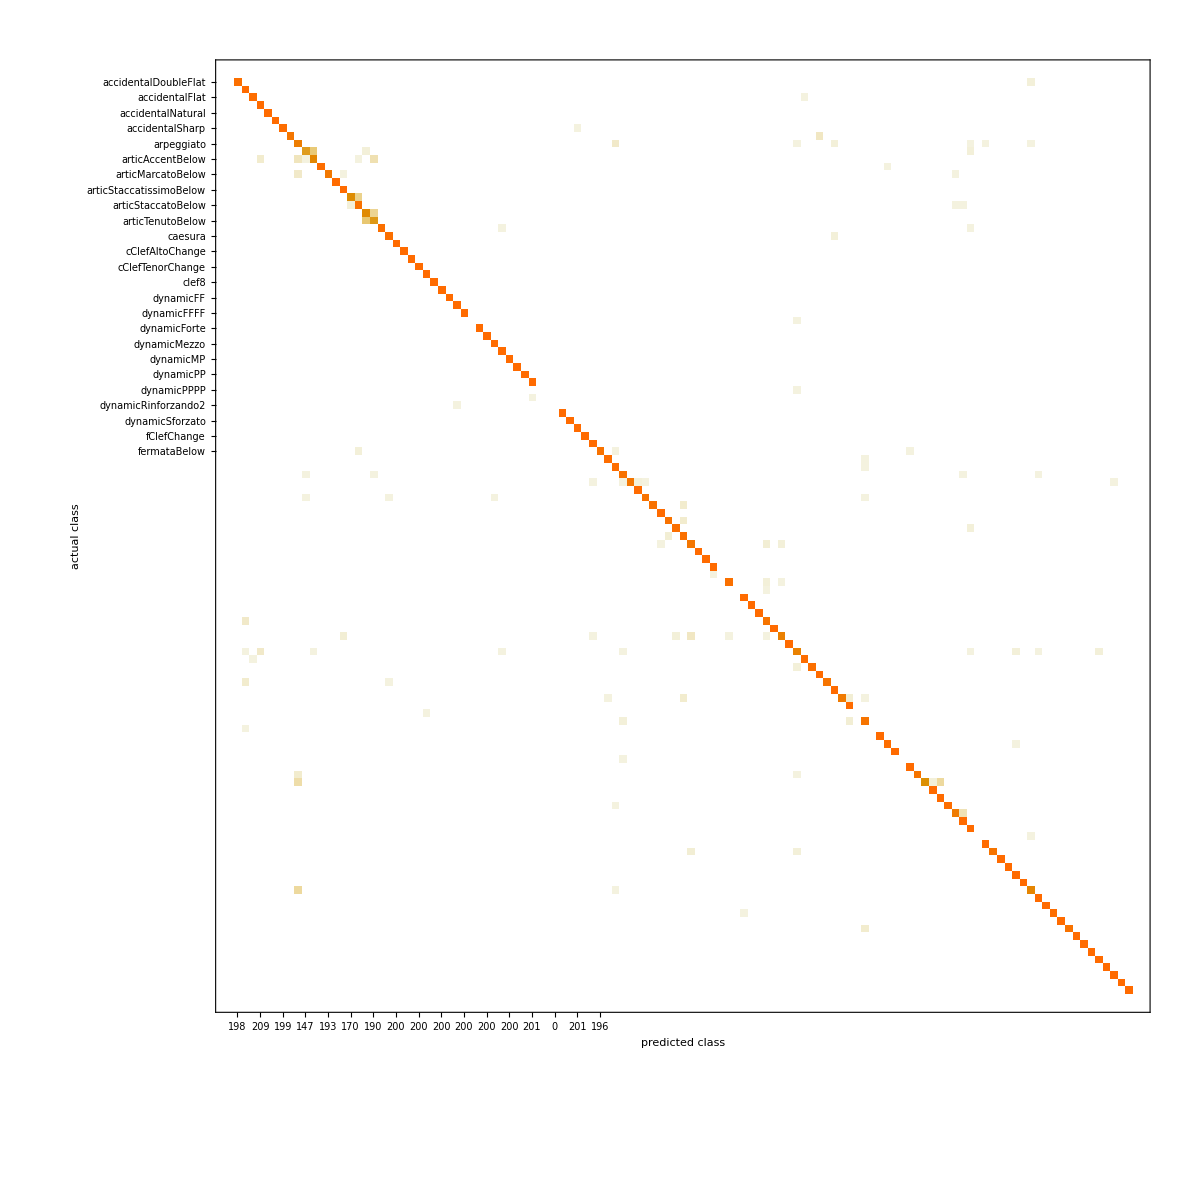

```mathematica
cm["ConfusionMatrixPlot"]
```

## Testing It

Original Image:

```mathematica
staffs⟦8⟧
```

-Graphics-

Trimmed bounding boxes:

```mathematica
bboxesTrimmed=First@ImageTrim[ImageResize[staffs⟦8⟧,{4096,1024}],{Rectangle@@8#}]&/@Select[bboxes,Area[Rectangle@@#]≥25&]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Resizing the trimmed images:

```mathematica
resizedBBoxTrimmed=ImageResize[#,{64,64}]&/@bboxesTrimmed
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Classifying them:

```mathematica
classified=symbolClassifier[(*Binarize@Blur@*)#(*,"TopProbabilities"*)]&/@resizedBBoxTrimmed;
```

```mathematica
Thread[{(*Binarize@Blur@*)#&/@#1,#2}&[resizedBBoxTrimmed,classified]]//TableForm
```

-Graphics- | accidentalNatural
-Graphics- | restHalf
-Graphics- | restHalf
-Graphics- | flag64thDown
-Graphics- | noteheadBlack
-Graphics- | flag32ndDown
-Graphics- | flag32ndDown
-Graphics- | timeSig1
-Graphics- | flag64thDown
-Graphics- | flag16thUp
-Graphics- | noteheadBlack
-Graphics- | noteheadBlack
-Graphics- | noteheadBlack
-Graphics- | restHalf
-Graphics- | noteheadBlackSmall
-Graphics- | noteheadBlack
-Graphics- | noteheadBlack
-Graphics- | gClef
-Graphics- | noteheadBlack
-Graphics- | noteheadBlack
-Graphics- | gClef
-Graphics- | restHalf
-Graphics- | noteheadBlack
-Graphics- | noteheadBlack
-Graphics- | restHBar
-Graphics- | timeSig4
-Graphics- | graceNoteAcciaccaturaStemUp

## Parsing the Sheet Music

Get the bounding boxes associated with what symbol they contain:

```mathematica
bboxesClassified=Thread[#1->#2&[Select[Rectangle@@#&/@bboxes,Area[#]≥25&],classified]]
```

{Rectangle[{289.,70.},{292.,81.}]→accidentalNatural,Rectangle[{214.,69.},{219.,80.}]→restHalf,Rectangle[{454.,69.},{459.,80.}]→restHalf,Rectangle[{416.,68.},{422.,79.}]→flag64thDown,Rectangle[{436.,69.},{441.,79.}]→noteheadBlack,Rectangle[{43.,69.},{48.,94.}]→flag32ndDown,Rectangle[{48.,56.},{53.,78.}]→flag32ndDown,Rectangle[{392.,59.},{397.,76.}]→timeSig1,Rectangle[{472.,65.},{478.,74.}]→flag64thDown,Rectangle[{268.,64.},{272.,72.}]→flag16thUp,Rectangle[{64.,58.},{69.,70.}]→noteheadBlack,Rectangle[{95.,58.},{100.,70.}]→noteheadBlack,Rectangle[{134.,59.},{139.,70.}]→noteheadBlack,Rectangle[{156.,59.},{162.,70.}]→restHalf,Rectangle[{177.,61.},{183.,70.}]→noteheadBlackSmall,Rectangle[{194.,58.},{199.,70.}]→noteheadBlack,Rectangle[{118.,59.},{124.,69.}]→noteheadBlack,Rectangle[{28.,29.},{40.,102.}]→gClef,Rectangle[{244.,55.},{250.,64.}]→noteheadBlack,Rectangle[{341.,55.},{346.,64.}]→noteheadBlack,Rectangle[{363.,55.},{368.,64.}]→gClef,Rectangle[{378.,43.},{382.,56.}]→restHalf,Rectangle[{325.,45.},{330.,55.}]→noteheadBlack,Rectangle[{284.,45.},{289.,54.}]→noteheadBlack,Rectangle[{95.,39.},{100.,53.}]→restHBar,Rectangle[{299.,40.},{305.,50.}]→timeSig4,Rectangle[{176.,40.},{181.,49.}]→graceNoteAcciaccaturaStemUp}

## Getting the Notes

Select bounding boxes for the black notes:

```mathematica
notes=Keys@Select[bboxesClassified,Values@#=="noteheadBlack"&]
```

{Rectangle[{436.,69.},{441.,79.}],Rectangle[{64.,58.},{69.,70.}],Rectangle[{95.,58.},{100.,70.}],Rectangle[{134.,59.},{139.,70.}],Rectangle[{194.,58.},{199.,70.}],Rectangle[{118.,59.},{124.,69.}],Rectangle[{244.,55.},{250.,64.}],Rectangle[{341.,55.},{346.,64.}],Rectangle[{325.,45.},{330.,55.}],Rectangle[{284.,45.},{289.,54.}]}

Get their centroids:

```mathematica
noteCentroids=RegionCentroid/@notes
```

{{438.5,74.},{66.5,64.},{97.5,64.},{136.5,64.5},{196.5,64.},{121.,64.},{247.,59.5},{343.5,59.5},{327.5,50.},{286.5,49.5}}

Plot them:

```mathematica
Show[ImageResize[staffs⟦8⟧,{512,128}],ListPlot[noteCentroids]]
```

-Graphics-

## Getting the Clef

Get all the clefs in the staff:

```mathematica
clef=Select[bboxesClassified,MemberQ[{"gClef","gClefChange","fClef","fClefChange","cClefAlto","cClefTenor","cClefAltoChange","cClefTenorChange"},Values@#]&]
```

{Rectangle[{28.,29.},{40.,102.}]→gClef,Rectangle[{363.,55.},{368.,64.}]→gClef}

## Getting the Rests

Select annotated bounding boxes for the rests:

```mathematica
rests=Select[bboxesClassified,MemberQ[{"restMaxima","restLonga","restDoubleWhole","restWhole","restHalf","restQuarter","rest8th","rest16th","rest32nd","rest64th","rest128th","restHBar"},Values@#]&]
```

{Rectangle[{214.,69.},{219.,80.}]→restHalf,Rectangle[{454.,69.},{459.,80.}]→restHalf,Rectangle[{156.,59.},{162.,70.}]→restHalf,Rectangle[{378.,43.},{382.,56.}]→restHalf,Rectangle[{95.,39.},{100.,53.}]→restHBar}

Put them in the correct notation:

```mathematica
restsNotation=SheetMusicRest[RegionCentroid[Keys@#],Values@#]&/@rests
```

{SheetMusicRest[{216.5,74.5},restHalf],SheetMusicRest[{456.5,74.5},restHalf],SheetMusicRest[{159.,64.5},restHalf],SheetMusicRest[{380.,49.5},restHalf],SheetMusicRest[{97.5,46.},restHBar]}

## Pitching the Notes

To find the note’s pitch, we need to compare its distance from the bottom of the staff in relation to the distance between the staff lines with some reference pitch given by the clef.

PitchNumber finds the distance from the note to the bottom of the image, taking into consideration the distance between the staff lines. However, before that can be done, we need to resize everything to the same dimensions as the bounding boxes (512 by 128); for this, we find a resize factor, and multiply them anywhere that data not from the bounding boxes come in.

Distance between the staff lines in the resized images (constant since the staff trimming from the beginning is constant as well)

```mathematica
δ=10
```

10

```mathematica
resizeFactor=128/ImageDimensions[staffs⟦8⟧]⟦2⟧
```

32/75

```mathematica
PitchNumber[noteCentroid_,δ_,bottom_] := (noteCentroid⟦2⟧-bottom)/(0.5δ)
```

```mathematica
naturalNotes = Flatten[Table[#<>ToString[i]&/@{"A","B","C","D","E","F","G"},{i,1,7}],1]
```

{A1,B1,C1,D1,E1,F1,G1,A2,B2,C2,D2,E2,F2,G2,A3,B3,C3,D3,E3,F3,G3,A4,B4,C4,D4,E4,F4,G4,A5,B5,C5,D5,E5,F5,G5,A6,B6,C6,D6,E6,F6,G6,A7,B7,C7,D7,E7,F7,G7}

In PitchToLetter, we compare the result of a note’s PitchNumber with a clef’s PitchNumber, naming the note along the way:

```mathematica
PitchToLetter[pitchNumber_,referenceNumber_,referenceLetter_] := RotateLeft[naturalNotes,FirstPosition[naturalNotes,referenceLetter]-1]⟦Round[pitchNumber-referenceNumber]+1⟧
```

We know from the way that we trimmed the staff images that the staff bottom has the Y coordinate of 2.25 Δ in the original image. Hence, to find the pitch, we just need to compare the notes to that with the resize factor applied, along with a clef:

```mathematica
pitchNumbers=PitchNumber[#,δ,resizeFactor 2.25 Δ]&/@SortBy[noteCentroids,#⟦1⟧&]
```

{3.96529,3.96529,3.96529,4.06529,3.96529,3.06529,1.06529,1.16529,3.06529,5.96529}

```mathematica
noteLetters=PitchToLetter[#,0,"E4"]&/@pitchNumbers
```

{B5,B5,B5,B5,B5,A5,F4,F4,A5,D5}

```mathematica
pitchedNotes=Thread[SheetMusicNote[#2,#1]&[noteLetters,SortBy[noteCentroids,#⟦1⟧&]]]
```

{SheetMusicNote[{66.5,64.},B5],SheetMusicNote[{97.5,64.},B5],SheetMusicNote[{121.,64.},B5],SheetMusicNote[{136.5,64.5},B5],SheetMusicNote[{196.5,64.},B5],SheetMusicNote[{247.,59.5},A5],SheetMusicNote[{286.5,49.5},F4],SheetMusicNote[{327.5,50.},F4],SheetMusicNote[{343.5,59.5},A5],SheetMusicNote[{438.5,74.},D5]}

## Final Parsing

The parsing in here is so simple that it’s just sorting:

```mathematica
NotationCentroid[SheetMusicNote[c_,_]] := c
```

```mathematica
NotationCentroid[SheetMusicRest[c_,_]] := c
```

```mathematica
ParseSheetMusic[pitchedNotes_,rests_] := SheetMusic@SortBy[Join[pitchedNotes,restsNotation],NotationCentroid[#]⟦1⟧&]
```

```mathematica
ParseSheetMusic[pitchedNotes,restsNotation]
```

SheetMusic[{SheetMusicNote[{66.5,64.},B5],SheetMusicNote[{97.5,64.},B5],SheetMusicRest[{97.5,46.},restHBar],SheetMusicNote[{121.,64.},B5],SheetMusicNote[{136.5,64.5},B5],SheetMusicRest[{159.,64.5},restHalf],SheetMusicNote[{196.5,64.},B5],SheetMusicRest[{216.5,74.5},restHalf],SheetMusicNote[{247.,59.5},A5],SheetMusicNote[{286.5,49.5},F4],SheetMusicNote[{327.5,50.},F4],SheetMusicNote[{343.5,59.5},A5],SheetMusicRest[{380.,49.5},restHalf],SheetMusicNote[{438.5,74.},D5],SheetMusicRest[{456.5,74.5},restHalf]}]